.

```mathematica
sys2 := {D[R[t],t]==k0+k1*S  - k2*R[t]}(*0de*)
```

```mathematica
parm = {k0->0.01, k1->1 , k2-> 5};(*parameter*)
```

```mathematica
List@@sys2[[1]][[2]]
```

{k0,k1 S,-k2 R[t]}

```mathematica
tmp1 = Cases[List@@sys2[[1]][[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]]
```

{-k2 R[t]}

```mathematica
deg2 = - Plus@@tmp1(*negative part*)
```

k2 R[t]

```mathematica
prod2 = Plus@@Complement[List@@sys2[[1]][[2]],tmp1];(*positive part*)
```

```mathematica
Plot[{(prod2 /. parm) /. S->1,(prod2 /. parm) /. S->2,(prod2 /. parm) /. S->3, deg2 /. parm},{R[t],0,1},Frame->True,PlotRange->{{0,1},{0,5}}, PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},Black},FrameLabel->{"R","Rate"},LabelStyle->{GrayLevel[0],Bold}]
```

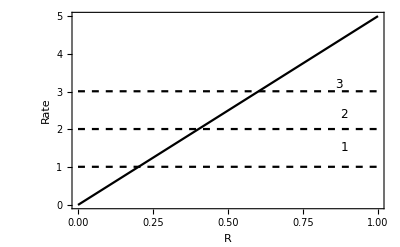

```mathematica
b1=Solve[sys2[[1]][[2]]==0/.parm,R[t]];(*nullclines*)
```

```mathematica
p1=Plot[Evaluate[{R[t]/.b1[[1]]}],{S,0,15},PlotRange->{{0,3},{0,0.7}},PlotRangeClipping->True,Frame->True,FrameLabel->{"Signal","Response"},LabelStyle->{GrayLevel[0],Bold}]
```

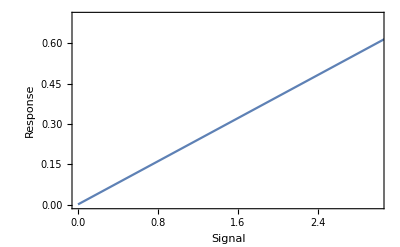

```mathematica
Show[p1,PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```